# WSS17 Project

```mathematica
init:=CellularAutomaton[
<|"Dimension"->3,"GrowthCases"->{5,10}|>,
{
{{{0,0,0},{0,1,0},{0,0,0}},
{{0,1,0},{1,1,1},{0,1,0}},
{{0,0,0},{0,1,0},{0,0,0}}},
0
},
{{{2}}}
]
```

```mathematica
init
```

{{{0,0,0,0,0},{0,0,0,0,0},{0,0,1,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,1,0,0},{0,1,1,1,0},{0,0,1,0,0},{0,0,0,0,0}},{{0,0,1,0,0},{0,1,1,1,0},{1,1,1,1,1},{0,1,1,1,0},{0,0,1,0,0}},{{0,0,0,0,0},{0,0,1,0,0},{0,1,1,1,0},{0,0,1,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,1,0,0},{0,0,0,0,0},{0,0,0,0,0}}}

```mathematica
cubelist[n_]:=Table[
Graphics3D[Cuboid/@Position[
CellularAutomaton[
<|"Dimension"->3,"GrowthCases"->{5}|>,
{
init,
0
},
{{{i}}}
],
1]
],
{i,0,n}
]
```

```mathematica
cubeiter[n_]:=Graphics3D[Cuboid/@Position[
CellularAutomaton[
<|"Dimension"->3,"GrowthCases"->{5}|>,
{
init,
0
},
{{{n}}}
],
1]
]
```

```mathematica
Table[
Graphics3D[Cuboid/@Position[
CellularAutomaton[
<|"Dimension"->3,"GrowthDecayCases"->{{5},{11}}|>,
{
init,
0
},
{{{i}}}
],
1]
],
{i,0,10}
]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
LatticeData["HexagonalLattice","Image"]
Normal[LatticeData["HexagonalLattice","Basis"]]
```

Missing[NotApplicable]

{{-1,1},{0,-1}}

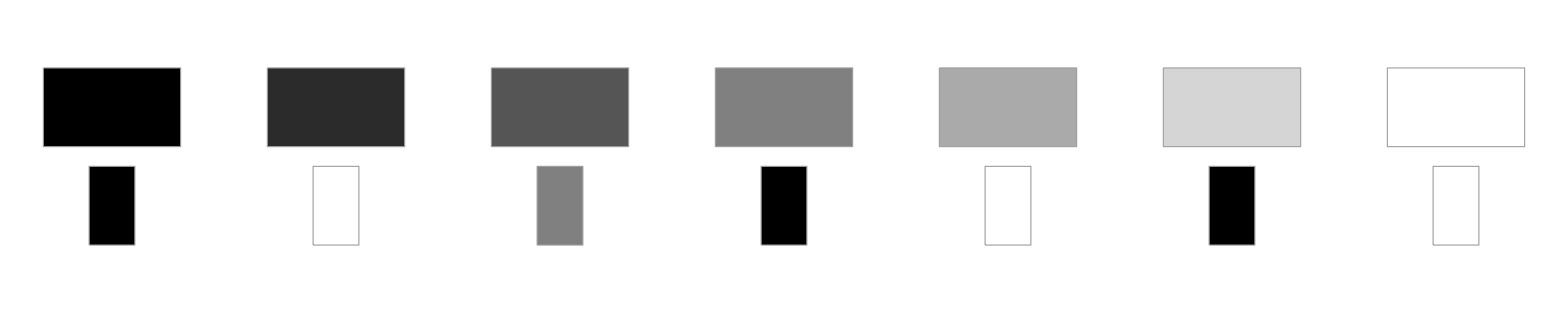

```mathematica
RulePlot[CellularAutomaton[{1599,{3,1}}]] (* totalistic *)
```

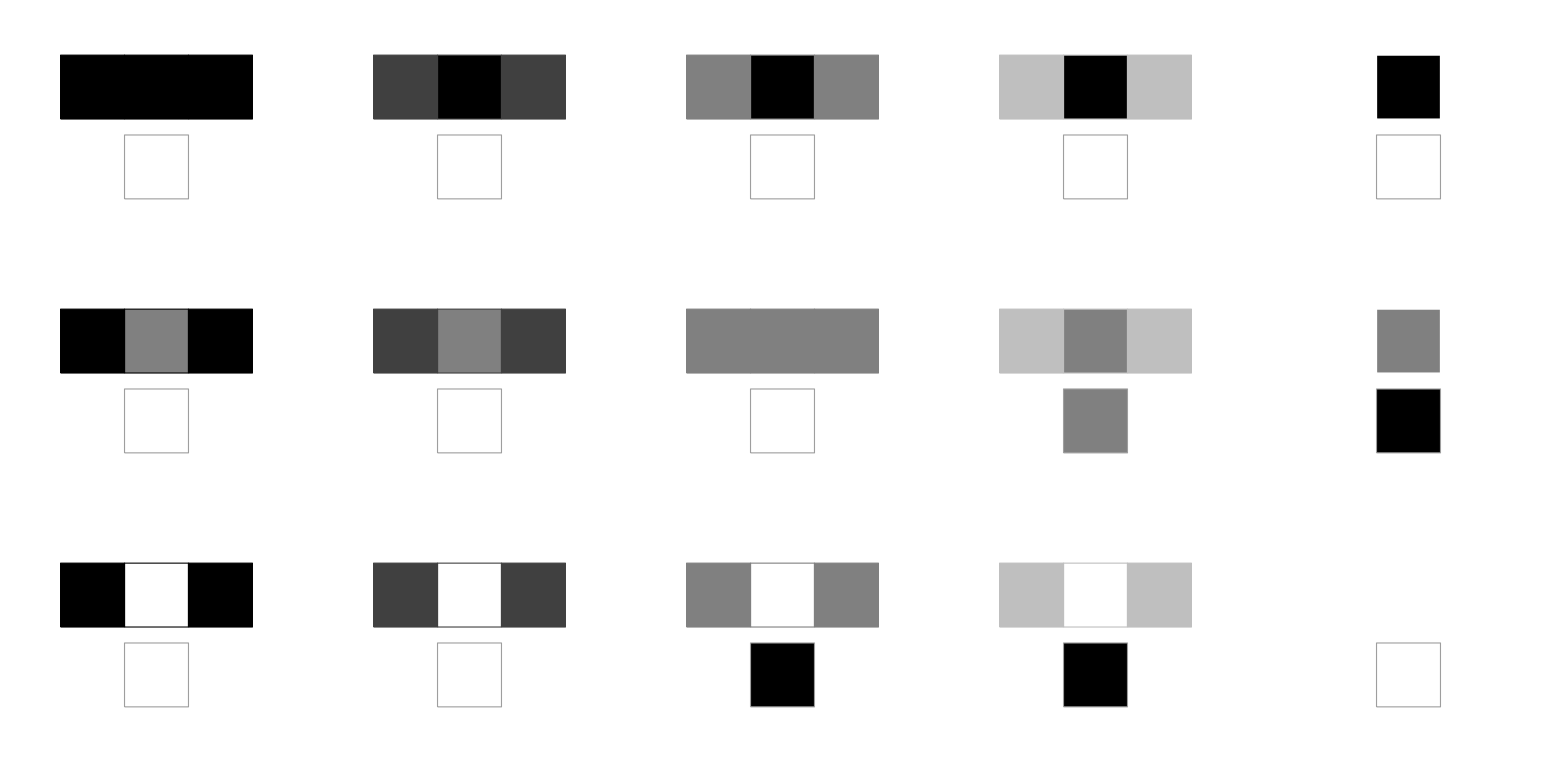

```mathematica
RulePlot[CellularAutomaton[{1599,{3,{3,1,3}}}]] (* outer-totalistic *)
```

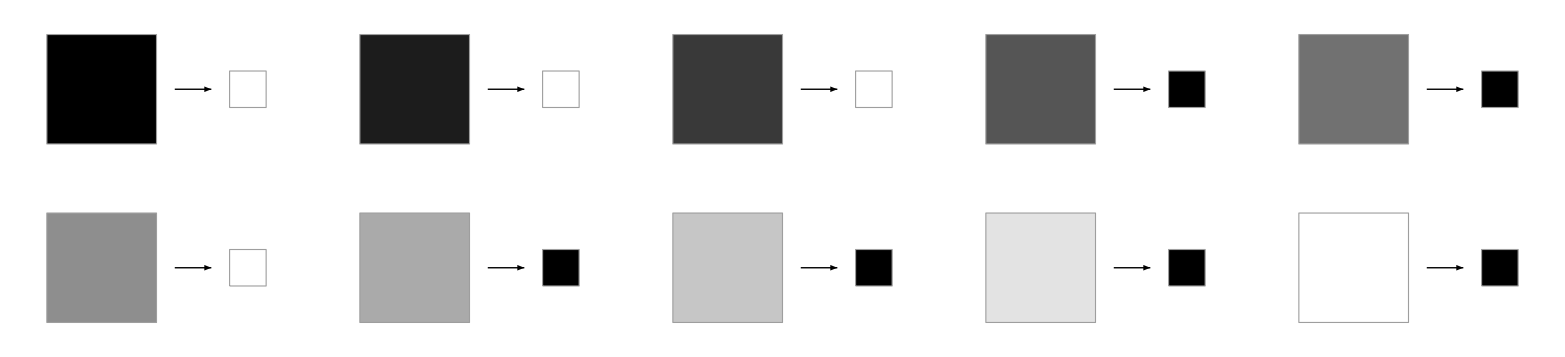

```mathematica
RulePlot[CellularAutomaton[{111,{2,{{1,1,1},{1,1,1},{1,1,1}}},{1,1}}]] (* totalistic *)
```

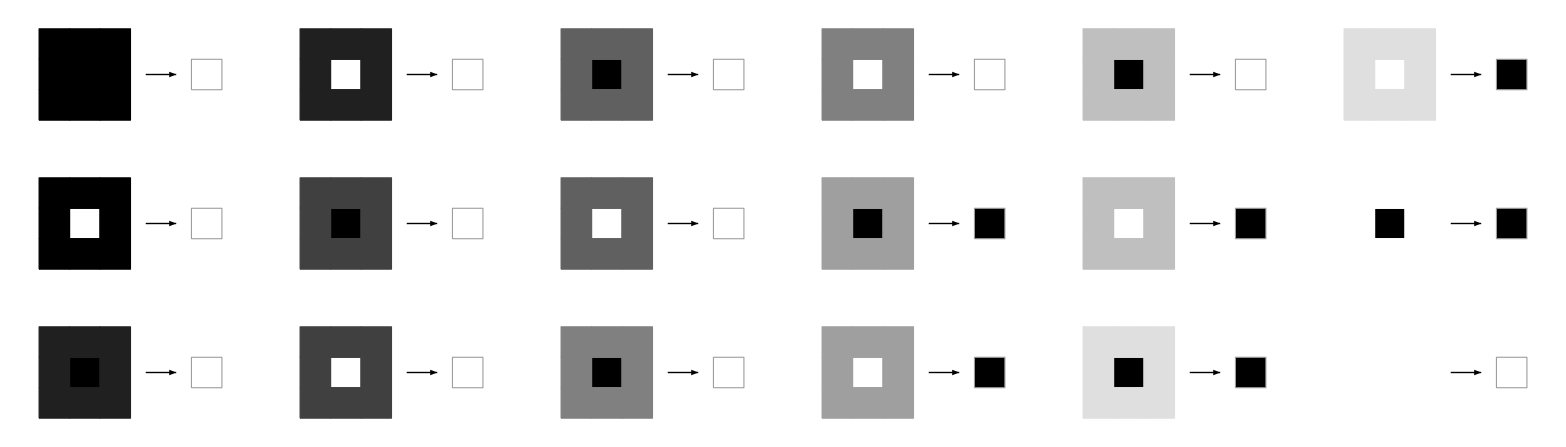

```mathematica
RulePlot[CellularAutomaton[{222,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}}]] (* outer-totalistic *)
```

JOBS: 
create 2d hexagonal lattice
create a generalized function that takes matrix, num. iterations, and rule as input for 2d & 3d;
can create 3d hexagonal prism by using coordinates, appending, and connecting with lines- then define

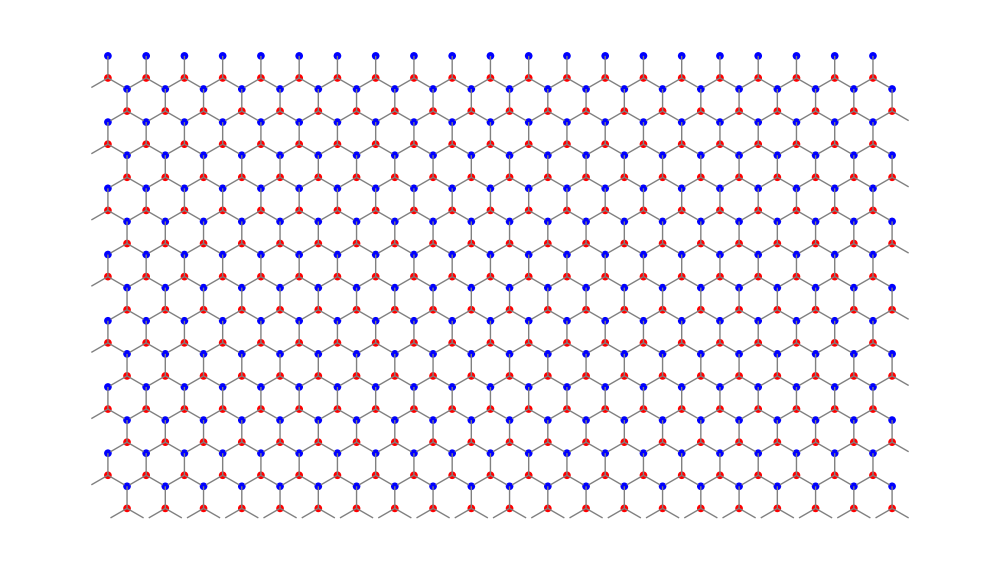

```mathematica
unitCell[x_,y_]:={Red,Disk[{x,y},0.1],
Blue,Disk[{x,y+2/3 Sin[120 Degree]},0.1],
Gray,,Line[{{x,y},{x,y+2/3 Sin[120 Degree]}}],Line[{{x,y},{x+Cos[30 Degree]/2,y-Sin[30 Degree]/2}}],Line[{{x,y},{x-Cos[30 Degree]/2,y-Sin[30 Degree]/2}}]}

Graphics[
Block[
{unitVectA={Cos[120 Degree],Sin[120 Degree]},
unitVectB={1,0}},
Table[
unitCell@@(unitVectA j+unitVectB k),{j,1,14},{k,Ceiling[j/2],20+Ceiling[j/2]}
]
],
ImageSize->1000]
```

```mathematica
Clear[hex,twohex,twohex1,threehex]
hex=CirclePoints[6]
twohex=Map[Append[#,0]&,hex]
twohex1=Map[Append[#,1]&,hex]
threehex=Append[twohex,twohex1[[1]]]
```

{{1/2,-(√3)/2},{1,0},{1/2,(√3)/2},{-1/2,(√3)/2},{-1,0},{-1/2,-(√3)/2}}

{{1/2,-(√3)/2,0},{1,0,0},{1/2,(√3)/2,0},{-1/2,(√3)/2,0},{-1,0,0},{-1/2,-(√3)/2,0}}

{{1/2,-(√3)/2,1},{1,0,1},{1/2,(√3)/2,1},{-1/2,(√3)/2,1},{-1,0,1},{-1/2,-(√3)/2,1}}

```mathematica
Internal`CellularAutomatonRuleLookup[<|"RuleNumber"->679458,"Colors"->3|>]
```

{679458,3,{1}}

```mathematica
Length[{1,0,0,{1,0,0}}]
```

4

## Hexagonal Grid

```mathematica
Clear[vertexFunc]

vertexFunc=Compile[{{para,_Real,1}},Module[{center,ratio},center=para[[1;;2]];
ratio=para[[3]];
{Re[#],Im[#]}+{{1,-(1/2)},{0,Sqrt[3]/2}}.Reverse[{-1,1} center+{3,0}]&/@(ratio 1/Sqrt[3] E^(I π/6) E^(I Range[6] π/3))],RuntimeAttributes->{Listable},Parallelization->True,RuntimeOptions->"Speed"
(*,CompilationTarget->"C"*)];

Clear[displayfunc]
displayfunc[array_,ratio_]:=Graphics[{FaceForm[{ColorData["DeepSeaColors"][3]}],EdgeForm[{ColorData["DeepSeaColors"][4]}],Polygon[vertexFunc[Append[#,ratio]]&/@Position[array,1]]},Background->ColorData["DeepSeaColors"][0]]
```

```mathematica
stateSet=Tuples[{0,1},6]//Rest
```

{{0,0,0,0,0,1},{0,0,0,0,1,0},{0,0,0,0,1,1},{0,0,0,1,0,0},{0,0,0,1,0,1},{0,0,0,1,1,0},{0,0,0,1,1,1},{0,0,1,0,0,0},{0,0,1,0,0,1},{0,0,1,0,1,0},{0,0,1,0,1,1},{0,0,1,1,0,0},{0,0,1,1,0,1},{0,0,1,1,1,0},{0,0,1,1,1,1},{0,1,0,0,0,0},{0,1,0,0,0,1},{0,1,0,0,1,0},{0,1,0,0,1,1},{0,1,0,1,0,0},{0,1,0,1,0,1},{0,1,0,1,1,0},{0,1,0,1,1,1},{0,1,1,0,0,0},{0,1,1,0,0,1},{0,1,1,0,1,0},{0,1,1,0,1,1},{0,1,1,1,0,0},{0,1,1,1,0,1},{0,1,1,1,1,0},{0,1,1,1,1,1},{1,0,0,0,0,0},{1,0,0,0,0,1},{1,0,0,0,1,0},{1,0,0,0,1,1},{1,0,0,1,0,0},{1,0,0,1,0,1},{1,0,0,1,1,0},{1,0,0,1,1,1},{1,0,1,0,0,0},{1,0,1,0,0,1},{1,0,1,0,1,0},{1,0,1,0,1,1},{1,0,1,1,0,0},{1,0,1,1,0,1},{1,0,1,1,1,0},{1,0,1,1,1,1},{1,1,0,0,0,0},{1,1,0,0,0,1},{1,1,0,0,1,0},{1,1,0,0,1,1},{1,1,0,1,0,0},{1,1,0,1,0,1},{1,1,0,1,1,0},{1,1,0,1,1,1},{1,1,1,0,0,0},{1,1,1,0,0,1},{1,1,1,0,1,0},{1,1,1,0,1,1},{1,1,1,1,0,0},{1,1,1,1,0,1},{1,1,1,1,1,0},{1,1,1,1,1,1}}

```mathematica
gatherTestFunc=Function[lst,Union[Join[RotateLeft[lst,#-1]&/@Flatten[Position[lst,1]],RotateLeft[Reverse[lst],#-1]&/@Flatten[Position[Reverse[lst],1]]]]];

stateClsSet=Sort/@Gather[stateSet,gatherTestFunc[#1]==gatherTestFunc[#2]&];

stateClsSetHomogeneous=ArrayPad[#,{{0,12-Length@#},{0,0}}]&/@stateClsSet;
```

```mathematica
Clear[ruleFunc]

ruleFunc=With[{stateClsSetHomogeneous=stateClsSetHomogeneous,seedStore=RandomInteger[{0,1000},1000],pFreeze={1,0,0.6,0,0.3,0.15,0,0.2,0,0.2,0,0.8},pMelt={0,0.7,0.5,0.7,0.7,0.5,0.3,0.5,0.3,0.2,0.1,0}},Compile[{{neighborarry,_Integer,2},{step,_Integer}},Module[{cv,neighborlst,cls,rand},cv=neighborarry[[2,2]];
neighborlst={#[[1,2]],#[[1,3]],#[[2,3]],#[[3,2]],#[[3,1]],#[[2,1]]}&[neighborarry];
If[Total[neighborlst]==0,cv,cls=Position[stateClsSetHomogeneous,neighborlst][[1,1]];
SeedRandom[seedStore[[step+1]]];
rand=RandomReal[];
Boole@If[cv==0,rand<pFreeze[[cls]],rand>pMelt[[cls]]]]],(*CompilationTarget->"C",*)RuntimeAttributes->{Listable},Parallelization->True,RuntimeOptions->"Speed"]];
```

```mathematica
dataSet=Module[{rule,initM={{{0,0,0},{0,1,0},{0,0,0}},0},rspec={1,1},tmin=0,tmax=100,dt=1},rule={ruleFunc,{},rspec};
CellularAutomaton[rule,initM,{{tmin,tmax,dt}}]];//AbsoluteTiming

Animate[Rotate[displayfunc[dataSet[[k]],.8],90 °],{k,1,Length[dataSet],1},AnimationDirection->ForwardBackward,AnimationRunning->False,DisplayAllSteps->True]
```

{26.6567,Null}